# Wolfram High School Summer Camp Challenges

Thank you for submitting your application to the 2020 Wolfram High School Summer Camp. As the next step in your application process, you must answer three of the questions below. Your response is due two weeks from the received date of this email.
You must answer at least three questions to be considered for the program. You are free to answer as many questions as you wish.
Your answers to these questions help us understand how you think about solving challenges and whether you are able to communicate your thought process with clarity and precision. Use as much space as you need to provide your answers.

## Instructions

For each coding challenge that you answer, please do the following:

Before you start coding: Write no more than 100 words about how you intend to approach the problem.

Solve the problem in at least two different ways. Feel free to submit more solutions.

Check your solution by evaluating your code. If it works, that’s great. If it doesn’t, that’s great too! We care more about your thought processes than we do about your answers.

In order for a solution to “work”, we should be able to run it in one execution. This will generally mean creating a function which takes the specified input and returns the expected result.

Write no more than 400 words describing:

How you went about solving the challenge.

What resources you used to solve the challenge.

What was the hardest part about solving this challenge.

How your solutions differ from each other.

When you are done:

Save this file as: WSC_Your_Name _Problems_1_2_3

Replace Your_Name with your own name, and Problems_1_2_3 with the problems you completed.

Send the notebook back to us by email.

## Resources

["Wolfram Language Documentation"](https://reference.wolfram.com/language/)

["Elementary Introduction to Wolfram Language"](https://www.wolfram.com/language/elementary-introduction/2nd-ed/)

## Problem 1: Butterflied Strings (2 Complete)

### The Challenge

Join a string with it’s reversal

### More Details

To butterfly the string "Wolfram", take its reversal "marfloW" and join them to form "WolframmarfloW".

### What your Function Should Do

Write a function ButterflyString that takes a string input and returns the input joined with its reversal.

```mathematica
ButterflyString["Wolfram"]
```

WolframmarfloW

```mathematica
ButterflyString["butterfly"]
```

butterflyylfrettub

```mathematica
ButterflyString["race"]
```

raceecar

```mathematica
ButterflyString["Hello world!"]
```

Hello world!!dlrow olleH

### How do you intend to approach the problem?

I am going to use the StringReverse function to reverse the input string and then concatenate it to the input for one solution. For the second solution, I will attempt to manually program the reverse function and then simply adjoin the original input.

### Scratch Area

```mathematica
x=""
 For[i =1, i<=StringLength["test"], i++,x=StringJoin[x,StringTake["test", {-i,-i}]]]
Print[x]
```

```mathematica
ButterflyString[input_]:=Module[{x},x="";For[i =1, i<=StringLength[input], i++,x=StringJoin[x,StringTake[input,{-i,-i}]]]; x=StringJoin[input, x]];ButterflyString["test"]
```

testtset

### Solution 1

```mathematica
ButterflyString1[x_]:=StringJoin[x,StringReverse[x]]

ButterflyString1["test"]
```

testtset

### Solution 2

```mathematica
ButterflyString2[x_]:=Module[{y},y="";For[i =1, i<=StringLength[x], i++,y=StringJoin[y,StringTake[x,{-i,-i}]]];y=StringJoin[x, y]]

ButterflyString2["test"]
```

testtset

### How did you go about solving the challenge?

I researched how to reverse a string, how to concatenate strings, and how to define functions of multiple lines in the Mathematica language. From there, I simply put everything together and after a few minutes of trial and error, my unit tests seemed to pass.

### What resources did you use to solve the challenge?

I used the following three links to official documentation to find the correct syntax:
https://reference.wolfram.com/language/tutorial/DefiningFunctions.html
https://reference.wolfram.com/language/ref/StringReverse.html
https://reference.wolfram.com/language/ref/StringJoin.html.en

I used the following link to understand how to write a function using multiple lines:
https://mathematica.stackexchange.com/questions/138842/creating-a-multiline-function-with-localized-variables

### What was the hardest part about solving this challenge?

The most difficult part was implementing the StringReverse function from scratch. It was challenging to design a loop that can iterate through a string and reverse the characters.

### How do your solutions differ from each other? How are they similar?

They are similar in that they have essentially the same idea of reversing the string and then concatenating it to the original string. The difference is that in the second one, I attempted my own implementation of StringReverse rather than using the built in function.

## Problem 2: Fizz Buzz (2 Complete)

### The Challenge

Given a list of integers from 1 to n, write a function that replaces multiples of 3 with “fizz”, multiples of 5 with “buzz”, multiples of both 3 and 5 with “fizzbuzz” and leaves other numbers fixed.

### More Details

For example, the input 7 gives the list:

```mathematica
{1,2,"fizz",4,"buzz","fizz",7}
```

### What your Function Should Do

Write a function called FizzBuzz that takes a positive integer n. The function returns a list of the integers from 1 to n, with multiples of 3 replaced by "fizz", multiples of 5 replaced by "buzz" and multiples of both 3 and 5 replaced by "fizzbuzz".

```mathematica
FizzBuzz[20]
```

{1,2,fizz,4,buzz,fizz,7,8,fizz,buzz,11,fizz,13,14,fizzbuzz,16,17,fizz,19,buzz}

All instances of "fizz", "buzz" and "fizzbuzz" should be returned as strings and all other elements should be integers:

```mathematica
FizzBuzz[10]//InputForm
```

{1, 2, "fizz", 4, "buzz", "fizz", 7, 8, "fizz", "buzz"}

```mathematica
Head/@%
```

{Integer,Integer,String,Integer,String,String,Integer,Integer,String,String}

### How do you intend to approach the problem?

First, I would generate the list of the first n integers. Following that, I would iterate through the list and define conditions to check each integer’s remainder when divided by 3, 5 & 15, and then replace the integer accordingly. For my second solution, I will use a different matrix oriented approach to process the numbers.

### Scratch Area

```mathematica
x=Range[15]

For[i =1, i<= 15, i++,If[Mod[x[[i]], 3]==0 && Mod[x[[i]], 5]!=0,x[[i]]="fizz"]If[Mod[x[[i]], 3]!= 0 && Mod[x[[i]], 5] == 0,x[[i]]="buzz"]If[Mod[x[[i]], 15]==0,x[[i]]="fizzbuzz"]]

x
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

{1,2,fizz,4,buzz,fizz,7,8,fizz,buzz,11,fizz,13,14,fizzbuzz}

```mathematica
Floor[Divide[46, 15]]
```

3

```mathematica
x = {}

x=Append[x, {12}]

x = Append[x, {13}]

x
```

{}

{{12}}

{{12},{13}}

{{12},{13}}

### Solution 1

```mathematica
FizzBuzz1[n_Integer]/;n>0:=Module[{a=n},x=Range[a];For[i =1, i<= a, i++,If[Mod[x[[i]], 3]==0 && Mod[x[[i]], 5]!=0,x[[i]]="fizz"]If[Mod[x[[i]], 3]!= 0 && Mod[x[[i]], 5] == 0,x[[i]]="buzz"]If[Mod[x[[i]], 15]==0,x[[i]]="fizzbuzz"]];x]

FizzBuzz1[45]
```

{1,2,fizz,4,buzz,fizz,7,8,fizz,buzz,11,fizz,13,14,fizzbuzz,16,17,fizz,19,buzz,fizz,22,23,fizz,buzz,26,fizz,28,29,fizzbuzz,31,32,fizz,34,buzz,fizz,37,38,fizz,buzz,41,fizz,43,44,fizzbuzz}

### Solution 2

```mathematica
FizzBuzz2[n_Integer]/;n>0:=Module[{a=n},mat={};rows=Floor[Divide[a, 15]];For[i=1, i<=  rows, i++, mat = Append[mat, Range[45][[15*(i-1)+1;;15*i]]]];mat[[All, {3,6,9,12}]] = "fizz";mat[[All, {5,10}]] = "buzz";mat[[All, {15}]] = "fizzbuzz";If[Divide[a, 15]-rows>0,mat = Append[mat, Range[45][[15*rows+1;;a]]],];mat[[-1, Range[3, a -15*rows, 3]]] = "fizz";mat[[-1, Range[5, a -15*rows, 5]]] = "buzz";mat]

FizzBuzz2[30]
```

{{1,2,fizz,4,buzz,fizz,7,8,fizz,buzz,11,fizz,13,14,fizzbuzz},{16,17,fizz,19,buzz,fizz,22,23,fizz,buzz,26,fizz,28,29,fizzbuzz}}

### How did you go about solving the challenge?

For the first solution, I generated a list of n integers, and modified elements based on whether they’re factors of 3, 5, or both. I noticed that when you structure the integers as a n X 15 matrix certain columns are replaced with “fizz”, “buzz”, or “fizzbuzz”. I exploited this pattern and programmed a matrix approach.

### What resources did you use to solve the challenge?

I used the following six links to official documentation to find the correct syntax:
https://reference.wolfram.com/language/ref/If.html
https://reference.wolfram.com/language/ref/And.html
https://reference.wolfram.com/language/ref/Mod.html
https://reference.wolfram.com/language/howto/CreateAMatrix.html
https://reference.wolfram.com/language/ref/Append.html
https://reference.wolfram.com/language/tutorial/ManipulatingListsByTheirIndices.html

Lexical Scoping:
https://reference.wolfram.com/language/tutorial/VariablesInPureFunctionsAndRules.html

### What was the hardest part about solving this challenge?

I had trouble understanding lexical scoping and consequently experienced a lot of errors when it came to using the same variables in Module and in the function.

### How do your solutions differ from each other? How are they similar?

The second solution utilizes a more complex matrix approach that I believe is faster (would have to look into the code for built-in functions to confirm). The second solution doesn’t check divisibility for every element while the first one does. They are similar in that they start by generating a list of n integers before proceeding with their processes.

## Problem 3: Valid Parentheses (2 Complete)

### The Challenge

Determine if a string of only parentheses is properly closed.

### What your Function Should Do

(Parentheses are round brackets, like the ones around this sentence.)

Write a function ValidParentheses that determines if a string of only ( and ) is properly closed.

```mathematica
ValidParentheses["()"]
```

True

```mathematica
ValidParentheses["()()()"]
```

True

```mathematica
ValidParentheses["(())"]
```

True

```mathematica
ValidParentheses["(()))("]
```

False

```mathematica
ValidParentheses[")())"]
```

False

### How do you intend to approach the problem?

I initially thought to simply count the number of left and right parentheses and compare them (if they’re equal then it’s valid), but I quickly realized that this approach wouldn’t work because of a test case like “))((”, where it is clearly invalid, but the program would return True because the number of left and right parentheses are the same. To mitigate this issue, I thought of a recursive approach which involves deleting any occurrences of “()” until there is 0, 1, or 2 characters left.

### Scratch Area

```mathematica
Count[StringSplit["()()(((("], "("]

StringSplit["()()(((("]
```

0

{()()((((}

```mathematica
StringRiffle[Flatten[StringSplit["()))((","()"]], ""]
```

))((

### Solution 1

```mathematica
ValidParentheses1[p_String]:=Module[{a=p},If[StringTake[a, {1,1}]==")",False,While[StringLength[a]>2 || a == "()",a=StringRiffle[Flatten[StringSplit[a,"()"]], ""]]];If[StringLength[a]>0,False, True]]

ValidParentheses1["()(()())("]
```

False

### Solution 2

```mathematica
ValidParentheses2[p_String]:=Module[{a=p},a=Characters[a];If[a[[1]]==")",False,While[Length[a]>2 || a== {"(",")"},For[i=1,i<Length[a] ,i++,If[StringJoin[a[[i]], a[[i+1]]]== "()",a=Delete[a, i];a= Delete[a, i],] ]]];If[Length[a]>0,False, True]]

ValidParentheses2["()(()())"]
```

True

### How did you go about solving the challenge?

I instructed the program to look for any occurrences of “()” and deleting them recursively until there was 0, 1, or 2 characters left. If there were no characters left, the string would be a valid use of parentheses, but if there were any characters remaining, the use of parentheses would be invalid.

### What resources did you use to solve the challenge?

I used the following 4 links to official documentation to find correct syntax:
https://reference.wolfram.com/language/ref/StringSplit.html
https://reference.wolfram.com/language/tutorial/CharactersInStrings.html
https://reference.wolfram.com/language/guide/ConvertingBetweenExpressionsAndStrings.html
https://reference.wolfram.com/language/ref/StringRiffle.html

### What was the hardest part about solving this challenge?

It was difficult to get the control flow working smoothly since the program got somewhat complicated. I had to spend more time researching syntax and revising my program to finally get it working.

### How do your solutions differ from each other? How are they similar?

They employ basically the same process to determine the validity of the use of parentheses (recursive deletion), but the only difference is that I programmed a linear search for the second solution as opposed to using the built in StringRiffle function for the first.

## Problem 4: Country Chains (1 Complete)

### The Challenge

Given two countries, find the length of the shortest chain of bordering countries that connects them.

### What your Function Should Do

Write a function CountryChainLength that takes two country entity inputs and returns the length of the shortest chain of bordering countries that connects them. If no such path exists, return ∞.

```mathematica
CountryChainLength[Entity["Country","France"],Entity["Country","Ukraine"]]
```

3

An example of such a chain is France → Germany → Poland → Ukraine:

-Graphics-

Adjacent countries only need one step:

```mathematica
CountryChainLength[Entity["Country","China"],Entity["Country","Mongolia"]]
```

1

The bordering countries:

-Graphics-

Some need many steps:

```mathematica
CountryChainLength[Entity["Country","Canada"],Entity["Country","Argentina"]]
```

10

Visualize:

-Graphics-

### How do you intend to approach the problem?

I want to try to implement a graph that describes neighboring countries and then use an algorithm like Dijkstra’s to find the shortest path between two nations. However, I am not entirely sure how to generate a graph that describes neighboring countries or if it’s even possible to do this with Mathematica.

### Scratch Area

```mathematica
GeoGraphics[{Red,GeoPath[{Entity["Country","France"],LinguisticAssistant}] }]
```

-Graphics-

```mathematica
CountryData["France", "BorderingCountries"]
```

{Andorra,Belgium,Germany,Italy,Luxembourg,Monaco,Spain,Switzerland}

```mathematica
(*EntityList[EntityClass["Country","Countries"]]*)
```

```mathematica
countrylist=EntityList[EntityClass["Country","Countries"]];
countrynet = {};
countrynet2=<||>;
For[i=1, i≤ Length[countrylist],i++,For[v=1, v≤Length[CountryData[countrylist[[i]], "BorderingCountries"]],v++,countrynet2[countrylist[[i]]]=CountryData[countrylist[[i]], "BorderingCountries"];countrynet=Append[countrynet, countrylist[[i]]-> CountryData[countrylist[[i]], "BorderingCountries"][[v]]]]];
Graph[countrynet]
Save["countrynet.wl",countrynet] 
Save["countrynet2.wl",countrynet2]
```

-Graphics-

```mathematica
Get["countrynet2.wl"][LinguisticAssistant]
```

{China,Iran,Pakistan,Tajikistan,Turkmenistan,Uzbekistan}

```mathematica
x={1->{2,4}, 2->{3,4}};
Graph[x];
y=<||>;
y[1]=2;
y
```

<|1→2|>

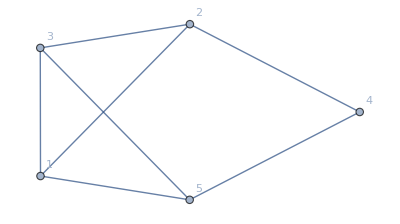

```mathematica
x={1<->2,1<->3, 2<-> 4, 5<->4,3<->5,2<->3};
x=Append[x, 1<-> 5];
Graph[x, VertexLabels->"Name"]
```

```mathematica
countrynet2[LinguisticAssistant]
```

{China,Iran,Pakistan,Tajikistan,Turkmenistan,Uzbekistan}

```mathematica
countrylist=EntityList[EntityClass["Country","Countries"]];
Djikstra[graph_,start_,dest_]:=Module[{x=graph,a=start,b=dest},unvisited={};visited={};distances={};]
```

```mathematica
x={3,4,5}
x=Delete[x,Position[x,3]]
```

{3,4,5}

{4,5}

### Solution 1

```mathematica
CountryChainLength1[c1_,c2_]:=
Module[{a=c1,b=c2},
If[Length[FindShortestPath[Graph[Get["countrynet.wl"]], a,b]]==0,Infinity,Length[FindShortestPath[Graph[Get["countrynet.wl"]], a,b]]-1]]

CountryChainLength1[LinguisticAssistant,LinguisticAssistant]
```

10

### Solution 2

```mathematica
CountryChainLength2[c1_,c2_]:=Module[{start=c1, end=c2,graph=Get["countrynet2.wl"]},unvisited=EntityList[EntityClass["Country","Countries"]];
distances=<||>;For[i=1,i≤ Length[unvisited],i++, If[unvisited[[i]]== start,distances[unvisited[[i]]]=0,distances[unvisited[[i]]]=Infinity]];While[Length[unvisited]≠ 0,minnode=None;For[i=1,i≤ Length[unvisited],i++,If[minnode==None,minnode=unvisited[[i]],If[distances[unvisited[[i]]]<distances[minnode],minnode=unvisited[[i]],]]];For[i=1,i≤ Length[graph[minnode]],i++,If[1+distances[minnode]<distances[graph[minnode][[i]]],distances[graph[minnode][[i]]]=1+distances[minnode],]];unvisited=Delete[unvisited,Position[unvisited,minnnode]];Print[Length[unvisited]]];
distances[end]]

CountryChainLength2[LinguisticAssistant,LinguisticAssistant]
```

### How did you go about solving the challenge?

I created a list describing bordering countries, which is cached in a file called “countrynet.wl”. This is cached because it takes a long time to generate the aforementioned list. After I cached the list, I reloaded it and converted it to Graph objects which can be used by the FindShortestPath function to locate the shortest path between to countries. For the second solution, I implemented Dijkstra’s algorithm on my own.

### What resources did you use to solve the challenge?

I used the following _ links to official documentation to find the correct syntax:
https://reference.wolfram.com/language/ref/EntityList.html
https://reference.wolfram.com/language/ref/CountryData.html
https://reference.wolfram.com/language/Combinatorica/ref/ShortestPath.html
https://reference.wolfram.com/language/ref/FindShortestPath.html
https://reference.wolfram.com/language/ref/Save.html

### What was the hardest part about solving this challenge?

It was difficult to translate my existing knowledge of Dijkstra’s into Mathematica because of the new syntax and control flow. It was also challenging to generate the Graph object that describes the bordering nations.

### How do your solutions differ from each other? How are they similar?

They both utilize shortest path algorithms, but I chose to implement my own for one of the solutions and use a builtin function for the other solution.

## Problem 5: Josephus Problem (2 Complete)

### The Challenge

Solve the Josephus problem: In a circle of n soldiers, every m^th soldier is executed. In what order are the soldiers executed?

### More Details

The problem is named after Flavius Josephus, from the first century. There is a variation of the problem that does not repeat anyone when counting off, so some soldiers escape being executed.

### What your Function Should Do

Define a function JosephusList that takes a pair of positive integers m and n and returns a list of the positions of the soldiers in the order that they are executed.

For example, If n==4 and m==1, the soldiers are executed in the order {1,2,3,4}:

```mathematica
JosephusList[4,1]
```

{1,2,3,4}

If n==4 and m==2, the list is {2,4,3,1}: 
count 1, 2, execute 2, leaving 1, 3, 4;
count 3, 4, execute 4, leaving 1, 3;
count 1, 3, execute 3, leaving 1;
count 1, 1, execute 1:

```mathematica
JosephusList[4,2]
```

{2,4,3,1}

If n==4 and m==4, 
count 1, 2, 3, 4, execute 4, leaving 1, 2, 3;
count 1, 2, 3, 1, execute 1, leaving 2, 3;
count 2, 3, 2, 3, execute 3, leaving 2;
count 2, 2, 2, 2, execute 2:

```mathematica
JosephusList[4,4]
```

{4,1,3,2}

```mathematica
JosephusList[30,4]
```

{4,8,12,16,20,24,28,2,7,13,18,23,29,5,11,19,26,3,14,22,1,15,27,10,30,21,17,25,9,6}

### How do you intend to approach the problem?

I hope to use a standard loop for the first solution that cycles through the list deleting any executed members and appending them to another list that’ll store the order of executions. For the second solution, I think I can use builtin functions from Combinatorica that I remember using in the past (Josephus and InversePermutation).

### Scratch Area

```mathematica
x=Range[4]
Drop[x,2]
Flatten[Append[x,x[[1;;2]]]]
RotateLeft[{2,3},3]
Mod[4,2]
```

{1,2,3,4}

{3,4}

{1,2,3,4,1,2}

{3,2}

0

4

3

```mathematica
step=2;
len=4;
alive=Range[len];
dead={};
If[Mod[step,Length[alive]]==0,pos=step-Mod[Length[alive],step],pos=Mod[step,Length[alive]]];
oldpos=pos;
While[Length[alive]>0,dead=Append[dead,alive[[pos]]];alive=Delete[alive,pos]; oldpos=pos;If[Mod[oldpos+step-1,Length[alive]]==0,pos=step,pos=Mod[oldpos+step-1,Length[alive]]];]
dead
alive
```

{2,3,1}

{4}

```mathematica
f[men_,skip_]:=Module[{n=men,k=skip},alive=Range[n];dead={};idx=1;While[Length[alive]>0,If[Mod[idx+k-1,Length[alive]]==0,idx=Length[alive],idx=Mod[idx+k-1,Length[alive]]];dead=Append[dead,alive[[idx]]];alive=Delete[alive,idx];];dead]
f[30,4]
```

{4,8,12,16,20,24,28,2,7,13,18,23,29,5,11,19,26,3,14,22,1,15,27,10,30,21,17,25,9,6}

### Solution 1

```mathematica
JosephusList1[men_Integer?Positive,skip_Integer?Positive]:= InversePermutation[Josephus[men,skip]]

JosephusList1[30,4]
```

{4,8,12,16,20,24,28,2,7,13,18,23,29,5,11,19,26,3,14,22,1,15,27,10,30,21,17,25,9,6}

### Solution 2

```mathematica
JosephusList2[men_Integer?Positive,skip_Integer?Positive]:= Module[{n=men,k=skip},alive=Range[n];dead={};idx=1;While[Length[alive]>0,If[Mod[idx+k-1,Length[alive]]==0,idx=Length[alive],idx=Mod[idx+k-1,Length[alive]]];dead=Append[dead,alive[[idx]]];alive=Delete[alive,idx];];dead]
JosephusList2[30,4]
```

{4,8,12,16,20,24,28,2,7,13,18,23,29,5,11,19,26,3,14,22,1,15,27,10,30,21,17,25,9,6}

### How did you go about solving the challenge?

For the first one I simply used builtin functions to get the correct output. For the second one, I thought about what kind of approach the builtin function took and implemented something that could possibly be similar. Basically what the function does is iterate through the list with alive soldiers and executes them using the step size and previous position (deleting them from the alive list and appending to dead list). Subsequent indices are calculated using the mod function. It continues this in a loop until all soldiers have been executed and returns the order to the user.

### What resources did you use to solve the challenge?

I used the following 2 links to official documentation to find correct syntax:
https://reference.wolfram.com/language/Combinatorica/ref/Josephus.html
https://reference.wolfram.com/language/Combinatorica/ref/InversePermutation.html

### What was the hardest part about solving this challenge?

It was hard to work with Mathematica arrays with the Mod functions since arrays start at 1 instead of 0 and Mod returns 0.

### How do your solutions differ from each other? How are they similar?

The solutions are essentially the same in that the approach is identical, but the first solution uses builtin libraries while the second is programmed with basic control flow and primitive functions.

## Problem 6: Anagram Words (2 Complete)

### The Challenge

An anagram is a word or phrase created by rearranging the letters of another word or phrase. Write a function that takes a word and uses the dictionary to return a list of anagrams.

### More Details

The possible anagrams of the word “past” are “spat”, “pats”, and “taps”. Find a way to identify anagrams of a given word.

### What your Function Should Do

Write a function called Anagrams that takes a word string and outputs the list of words in DictionaryLookup[] that are anagrams of the input, together with the original input. Give the result in alphabetical order.

```mathematica
Anagrams["burned"]
```

{burden,burned}

### How do you intend to approach the problem?

I plan on generating all permutations of the given string and then looking it up in the dictionary to see if it exists. If it does exist, it’ll keep it in the list of permutations, if not, it’ll remove it from the list. Seeing that this method is rather inefficient and has a runtime close to O(n!), I could probably do this more efficiently.

### Scratch Area

```mathematica
words=StringJoin /@Permutations[Characters["abc"]]

realwords=DeleteCases[DictionaryLookup /@ words, {}]
```

{abc,acb,bac,bca,cab,cba}

{{cab}}

```mathematica
WordData["good","Antonyms"]
```

{{good,Interjection}→{},{good,Noun,Artifact}→{},{good,Noun,Morality}→{evil},{good,Noun,Quality}→{bad},{good,Noun,Advantage}→{},{good,Adjective,Beneficial}→{},{good,Adjective,Full}→{},{good,Adjective,Near}→{},{good,Adjective,Complete}→{},{good,Adjective,Discriminating}→{},{good,Adjective,InForce}→{},{good,Adjective,Well}→{},{good,Adjective,Unspoilt}→{},{good,Adjective,Honest}→{},{good,Adjective,WellBehaved}→{bad},{good,Adjective,Redemptive}→{evil},{good,Adjective,Salutary}→{},{good,Adjective,Sound}→{},{good,Adjective,Serious}→{},{good,Adjective,Nice}→{},{good,Adjective,Right}→{},{good,Adjective,Pleasing}→{},{good,Adjective,Respectable}→{},{good,Adjective,Just}→{},{good,Adjective,Practiced}→{},{good,Adjective,Safe}→{},{good,Adverb,Well}→{},{good,Adverb,Thoroughly}→{}}

### Solution 1

```mathematica
Anagrams1[s_String]:=Module[{a=s},words=StringJoin /@Permutations[Characters[a]];realwords=Sort[Flatten[DeleteCases[DictionaryLookup /@ words, {}]]]]

Anagrams1["cater"]
```

{caret,cater,crate,react,trace}

### Solution 2

```mathematica
Anagrams2[s_String]:=Sort[Append[ResourceFunction["Anagrams"][s],s]]

Anagrams2["cater"]
```

{caret,carte,cater,crate,react,trace}

### How did you go about solving the challenge?

I used the following link to official documentation to find the correct syntax:
https://reference.wolfram.com/language/ref/Map.html

### What resources did you use to solve the challenge?

I had trouble learning how to appropriately utilize the map function/shorthand in Mathematica. I was familiar with its concept because it is used heavily in python, but it was somewhat challenging to learn the syntax for Mathematica.

### What was the hardest part about solving this challenge?

The most difficult part was thinking about quicker ways to solve the problem, but not finding any :(. I think an approach to potentially reduce runtime is to only generate permutations of the first few letters and then look those up in the dictionary and return any valid entries to the user. I’m still not fully convinced this would necessarily be faster because the program may be forced to check through more dictionary entries than permutations.

### How do your solutions differ from each other? How are they similar?

The first one simply generates every permutation of the word and checks if it exists in the dictionary, but the second one utilizes a builtin function. I looked into the function definition of the builtin function and realized they used a very similar generative approach. They differ because one is builtin and the other is programmed manually.

## Problem 7: Odds before Evens (2 Complete)

### The Challenge

Given a list of integers, rearrange them so that all of the odd integers appear before all of the even integers, without otherwise changing the order.

### More Details

For example, look at the following list:

```mathematica
{-1,2,8,-9,-2,-3,-6,-10,-8,5,7,9,7}
```

Rearranged, it would look like this:

```mathematica
{-1,-9,-3,5,7,9,7,2,8,-2,-6,-10,-8}
```

Apart from putting the odds in front, the order is the same.

### What your Function Should Do

Write a function called OddBeforeEven that takes a list of integers and outputs a list such that all odd integers from the given list appear before even integers, without rearranging the numbers in any other way.

```mathematica
OddBeforeEven[{-1,2,8,-9,-2,-3,-6,-10,-8,5,7,9,7}]
```

{-1,-9,-3,5,7,9,7,2,8,-2,-6,-10,-8}

### How do you intend to approach the problem?

I will iterate through the list and check the integer’s parity and append it to an even or odd list accordingly. Then I will simply adjoin both the even and odd list. Note that order is preserved since the iteration is done linearly.

### Scratch Area

```mathematica
nums = {-1,2,8,-9,-2,-3,-6,-10,-8,5,7,9,7}
odds ={}
evens={}
For[i=1,i≤Length[nums],i++,If[Mod[nums[[i]],2]==0,evens=Append[evens, nums[[i]]],odds=Append[odds,nums[[i]]]]]
Join[odds, evens]
```

{-1,2,8,-9,-2,-3,-6,-10,-8,5,7,9,7}

{}

{}

{-1,-9,-3,5,7,9,7,2,8,-2,-6,-10,-8}

### Solution 1

```mathematica
OddBeforeEven1[list:{__Integer}]:=
Module[{nums=list},
odds={};evens={};
For[i=1,i≤Length[nums],i++,If[Mod[nums[[i]],2]==0,evens=Append[evens, nums[[i]]],odds=Append[odds,nums[[i]]]]];
Join[odds, evens]
]

OddBeforeEven1[{-1,2,8,-9,-2,-3,-6,-10,-8,5,7,9,7}]
```

{-1,-9,-3,5,7,9,7,2,8,-2,-6,-10,-8}

### Solution 2

```mathematica
OddBeforeEven2[list:{__Integer}]:=
Join[Select[list, EvenQ], Select[listOddQ]]
OddBeforeEven1[{-1,2,8,-9,-2,-3,-6,-10,-8,5,7,9,7}]
```

{-1,-9,-3,5,7,9,7,2,8,-2,-6,-10,-8}

### How did you go about solving the challenge?

For the first one, I defined two sublists (one for even integers and one for odd integers), which would be updated as the program linearly iterates through the original list and classifies each integer based on its parity. For the second one, I used a builtin function to select the even and odd integers, which simplified things immensely.

### What resources did you use to solve the challenge?

I used the following link to official documentation to find the correct syntax:
https://reference.wolfram.com/language/ref/Select.html

### What was the hardest part about solving this challenge?

Programming the first solution and defining the control flow was challenging and finding the correct builtin function to simplify the task was also difficult.

### How do your solutions differ from each other? How are they similar?

The first one uses primitive functions to linearly iterate through the list and classify even and odd integers while the second one uses an in built function to select the even integers and odd integers. They are both similar in that they separate the original list into even and odd subsets before joining them back together to yield the solution.

## Problem 8: Most Roman Numerals (1 Complete)

### The Challenge

Write a function to find the first integer less than n with the longest representation in Roman numerals.

### More Details

Here are the numbers up to 15 in Roman numerals:

```mathematica
RomanNumeral[Range[15]]
```

{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV}

The longest of these are VIII and XIII.

### What your Function Should Do

Write a function called FindLongestRomanNumeral that takes as input a positive integer n and returns the first base-10 number less than or equal to n whose Roman numeral representation is the longest.

```mathematica
FindLongestRomanNumeral[100]
```

88

### How do you intend to approach the problem?

For the first solution, I’ll simply use brute force and list out every roman numeral in the specified range and select the longest one. For the second solution, I will try to notice a pattern in the data and exploit it to improve runtime and memory allocation.

### Scratch Area

```mathematica
x =StringLength /@ RomanNumeral[Range[100]]
max = Max[x]
Position[x, max]
```

{1,2,3,2,1,2,3,4,2,1,2,3,4,3,2,3,4,5,3,2,3,4,5,4,3,4,5,6,4,3,4,5,6,5,4,5,6,7,5,2,3,4,5,4,3,4,5,6,4,1,2,3,4,3,2,3,4,5,3,2,3,4,5,4,3,4,5,6,4,3,4,5,6,5,4,5,6,7,5,4,5,6,7,6,5,6,7,8,6,2,3,4,5,4,3,4,5,6,4,1}

8

{{88}}

```mathematica
StringLength /@ RomanNumeral[Range[12]]
Position[StringLength /@ RomanNumeral[Range[12]], ]
```

{1,2,3,2,1,2,3,4,2,1,2,3}

```mathematica
max=10000
testers={38,78,83,87,88}+If[IntegerLength[max]≤4,0,8*(10^(IntegerLength[max]-5)-1)/9*100]
If[IntegerLength[max]>3,x=StringLength /@ RomanNumeral[Join[Range[testers[[1]],max,10^(IntegerLength[max]-3)],]],RomanNumeral1[max]]
```

10000

{38,78,83,87,88}

### Solution 1

```mathematica
FindLongestRomanNumeral1[max_Integer?Positive]:=
Flatten[Position[StringLength /@ RomanNumeral[Range[max]], Max[StringLength /@ RomanNumeral[Range[max]]]]]
FindLongestRomanNumeral1[100000]
```

{84888,88888}

### Solution 2

```mathematica
FindLongestRomanNumeral2[max_Integer?Positive]:=
If[max<38,FindLongestRomanNumeral1[max],testers={38,78,83,87,88}+If[IntegerLength[max]≤3,0,8*(10^(IntegerLength[max]-2))]]
```

### How did you go about solving the challenge?

For the first solution, I designed a simple brute force algorithm that generates the range as a list of integers and then converts every integer to its Roman numeral representation. From there, it finds the longest string and returns the positions of the strings, which is ultimately the desired outputs. After running this for a few different ranges, I noticed that the largest numeral is generally always in the form _88, _38, _83, _78, _87. Hence, I decided to check numbers only in these forms.

### What resources did you use to solve the challenge?

I’ve used some of the previously mentioned resources (past problems). Nothing new!

### What was the hardest part about solving this challenge?

Trying to find a trend in the data and explaining it. Why is it that the longest Roman Numeral expressions correspond with numbers that end with 38, 78, 83, 87 or 88. How can I generalize this to numbers longer than 3 digits? These are some of the questions I struggled to find answers to. Consequently, I had even more trouble implementing the function.

### How do your solutions differ from each other? How are they similar?

The first one utilizes a simple and inefficient brute force algorithm to generate every possible Roman Numeral expression, while the second exploits a pattern discovered after implementing the first solution. I’m fairly certain the second method is faster because it considers less test cases, but I don’t know exactly how to prove that it accurately evaluates every case.

## Problem 9: Breaking the Caesar Cipher (2 Complete)

### The Challenge

The Caesar shift cipher encrypts a message by replacing each letter with a letter some fixed distance away from it in the alphabet. Write a function to decrypt a message that was enciphered using a Caesar shift.

### More Details

A cipher uses a "key" to disguise plaintext to make it unreadable. The Caesar shift cipher is one of the simplest and best-known methods of encryption. The key is a number between 1 and 25. The method is to shift each letter in the alphabet by n.

For example, with n=4, the letters are shifted four places over:

```mathematica
Thread[Alphabet[] -> RotateLeft[Alphabet[], 4]]
```

{a→e,b→f,c→g,d→h,e→i,f→j,g→k,h→l,i→m,j→n,k→o,l→p,m→q,n→r,o→s,p→t,q→u,r→v,s→w,t→x,u→y,v→z,w→a,x→b,y→c,z→d}

Using those rules lets you encrypt a message—for example, the word "retreat":

```mathematica
StringReplace["retreat", Thread[Alphabet[] -> RotateLeft[Alphabet[], 4]]]
```

vixviex

The end of the alphabet is wrapped around to the beginning ("z" → "d"):

```mathematica
StringReplace["fuzzy", Thread[Alphabet[] -> RotateLeft[Alphabet[], 4]]]
```

jyddc

To decrypt, you need to shift back. One way might be to try each of the 25 shifts and select the strings that are words in the dictionary. In this Challenge, the key is given.

### What your Function Should Do

Write a function called CaesarDecrypt that takes two arguments, an encrypted text in lowercase and a key, and outputs the decrypted message.

```mathematica
CaesarDecrypt["dbu", 1]
```

cat

### How do you intend to approach the problem?

I’ll obtain the association containing the key value pairs of each character of the alphabet and then decrypt the message by iterating through the string and modifying each character.

### Scratch Area

```mathematica
x=<|Thread[Alphabet[] -> RotateLeft[Alphabet[], 22]]|>
```

<|a→w,b→x,c→y,d→z,e→a,f→b,g→c,h→d,i→e,j→f,k→g,l→h,m→i,n→j,o→k,p→l,q→m,r→n,s→o,t→p,u→q,v→r,w→s,x→t,y→u,z→v|>

```mathematica
StringReplace["jyddc", Thread[Alphabet[] -> RotateLeft[Alphabet[], 22]]]
```

fuzzy

```mathematica
Characters["test"]
```

{t,e,s,t}

### Solution 1

```mathematica
CaesarDecrypt1[cipherText_String?LowerCaseQ,key_Integer]/;1≤key≤25:= StringReplace[cipherText, Thread[Alphabet[] -> RotateLeft[Alphabet[], 26-key]]]
CaesarDecrypt1["dbu",1]
```

cat

### Solution 2

```mathematica
CaesarDecrypt2[cipherText_String?LowerCaseQ,key_Integer]/;1≤key≤25:= Module[{str=cipherText, step=key},ans="";str=Characters[str];shifter= <|Thread[Alphabet[] -> RotateLeft[Alphabet[], 26-key]]|>;For[i=1,i≤ Length[str],i++, ans=StringJoin[ans,shifter[str[[i]]]]]; ans]

CaesarDecrypt2["dbu",1]
```

cat

### How did you go about solving the challenge?

For the first solution, I used a similar approach to the one described in the problem statement noticing that the way to decrypt the string is to set the key to 26-given. For the second one, I iterated through the entire string and shifted each character and appended it to the output until the loop was complete and returned the decoded string to the user.

### What resources did you use to solve the challenge?

I’ve used some of the previously mentioned resources (past problems). Nothing new!

### What was the hardest part about solving this challenge?

The hardest part was finding the key to correctly decode the strings. It took a bit of time to realize that the way to decode a string when given a key was to reapply the Caesar shift but with a key of 26-given.

### How do your solutions differ from each other? How are they similar?

They are similar in that they reapply a Caesar shift, but with a new key, but the first one is a little simpler because it doesn’t use an iterative solution, the second solution does.

## Problem 10: Write in Morse Code (2 Complete)

### The Challenge

Morse code is a way of transmitting text through a series of unique sounds or lights represented by dots and dashes, represented by “.” and “-“. Write a function that takes an English text and outputs the corresponding Morse code.

### More Details

One famous piece of Morse code is “... --- ...”, a distress signal for “SOS” that stands for “Save Our Souls”.

### What your Function Should Do

Write a function ToMorseCode that takes a string of English text and outputs the Morse code translation. Use "/" to separate words.

```mathematica
ToMorseCode["This is not a pipe"]
```

- .... .. ... / .. ... / -. --- - / .- / .--. .. .--. .

```mathematica
ToMorseCode["Wolfram Challenges"]
```

.-- --- .-.. ..-. .-. .- -- / -.-. .... .- .-.. .-.. . -. --. . ...

To avoid ambiguity, separate each character with a single whitespace character:

```mathematica
ToMorseCode["use spaces"]
```

..- ... . / ... .--. .- -.-. . ...

Here are all positions of whitespace characters in the previous example:

```mathematica
StringPosition[%," "]⟦All,1⟧
```

{4,8,10,12,16,21,24,29,31}

Treat uppercase and lowercase characters the same:

```mathematica
ToMorseCode["SAME"]
```

... .- -- .

```mathematica
ToMorseCode["same"]
```

... .- -- .

### How do you intend to approach the problem?

I will use an association of the morse code alphabet whose indices correspond to the standard alphabet and iterate through the input converting each character.

### Scratch Area

```mathematica
morseDict=<|"a"->".-","b"->"-...","c"->"-.-.","d"->"-..","e"->".","f"->"..-.","g"->"--.","h"->"....","i"->"..","j"->".---","k"->"-.-","l"->".-..","m"->"--","n"->"-.","o"->"---","p"->".--.","q"->"--.-","r"->".-.","s"->"...","t"->"-","u"->"..-","v"->"...-","w"->".--","x"->"-..-","y"->"-.--","z"->"--.."|>;
str=Characters[ToLowerCase["This"]];
ans="";
For[i=1,i≤Length[str],i++,If[str[[i]]==" ",ans=StringJoin[ans, "/ "],ans=StringJoin[ans,morseDict[str[[i]]], " "]]]
ans
```

- .... .. ...

```mathematica
StringReplace["same thing", Thread[Append[Alphabet[]," "] ->{".- ","-... ","-.-. ","-.. ",". ","..-. ","--. ",".... ",".. ",".--- ","-.- ",".-.. ","-- ","-. ","--- ",".--. ","--.- ",".-. ","... ","- ","..- ","...- ",".-- ","-..- ","-.-- ","--.. ", "/ "}]]
```

... .- -- . / - .... .. -. --.

```mathematica
Append[Alphabet[]," "]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z, }

### Solution 1

```mathematica
ToMorseCode1[text_String]:=Module[{str=Characters[ToLowerCase[text]]},ans="";morseDict=<|"a"->".-","b"->"-...","c"->"-.-.","d"->"-..","e"->".","f"->"..-.","g"->"--.","h"->"....","i"->"..","j"->".---","k"->"-.-","l"->".-..","m"->"--","n"->"-.","o"->"---","p"->".--.","q"->"--.-","r"->".-.","s"->"...","t"->"-","u"->"..-","v"->"...-","w"->".--","x"->"-..-","y"->"-.--","z"->"--..","1"->".----","2"->"..---","3"->"...--","4"->"....-","5"->".....","6"->"-....","7"->"--...","8"->"---..","9"->"----.","0"->"-----","."->".-.-.-",","->"--..--","!"->"-.-.--","?"->"..--.."|>;For[i=1,i≤Length[str],i++,If[str[[i]]==" ",ans=StringJoin[ans, "/ "],ans=StringJoin[ans,morseDict[str[[i]]], " "]]];ans]
ToMorseCode1["Wolfram Challenges"]
```

.-- --- .-.. ..-. .-. .- -- / -.-. .... .- .-.. .-.. . -. --. . ...

### Solution 2

```mathematica
ToMorseCode2[text_String]:=StringReplace[ToLowerCase[text], Thread[Append[Alphabet[]," "] ->{".- ","-... ","-.-. ","-.. ",". ","..-. ","--. ",".... ",".. ",".--- ","-.- ",".-.. ","-- ","-. ","--- ",".--. ","--.- ",".-. ","... ","- ","..- ","...- ",".-- ","-..- ","-.-- ","--.. ", "/ "}]]
ToMorseCode2["Wolfram Challenges"]
```

.-- --- .-.. ..-. .-. .- -- / -.-. .... .- .-.. .-.. . -. --. . ...

### How did you go about solving the challenge?

For the first solution I used an association and iterated through the input string modifying every character. For the second one, I used an approach similar to the one described in the problem statement of Caesar shift.

### What resources did you use to solve the challenge?

I’ve used some of the previously mentioned resources (past problems). Nothing new!

### What was the hardest part about solving this challenge?

The hardest part was coming up with two distinct solutions because when I initially read the problem I could only think of one way of doing it. It took some time to think about a second way of programming an answer.

### How do your solutions differ from each other? How are they similar?

They both replace each character the original input with the corresponding morse code counterpart. They’re different because the second one replaces every character of the string asynchronously while the second one iterates through the input string and changes it one character at a time.